## Looking at the subgraphs of alfa1 etc

```mathematica
allGraphs5[alfa1Key,"colofourrealnull"]
```

2 n12345-n1234x5-n135x24-n13x245+n13x24x5

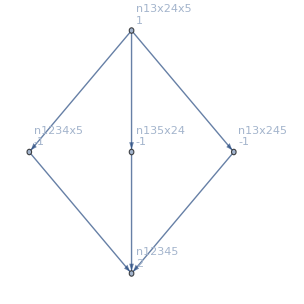

```mathematica
MobiusGraphBare[alfa1Key,allGraphs5]
```

```mathematica
Select[Keys[allGraphs5],allGraphs5[#,"colofourrealnull"]==n135x24-n12345&]
```

{36898}

```mathematica
With[{k=36898},Labeled[allGraphs5[k,"graph"],allGraphs5[k,"comp"]]]
```

-Graphics-GreaterEqual

```mathematica
Select[Keys[allGraphs5],allGraphs5[#,"colofourrealnull"]==n1234x5-n12345&]
```

{58288}

```mathematica
With[{k=58288},Labeled[allGraphs5[k,"graph"],allGraphs5[k,"comp"]]]
```

-Graphics-Greater

```mathematica
repsomething=First[Solve[Table[allGraphs5[k,"colofourrealnull"]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}],{n14x235,n124x35,n135x24,n13x245,n134x25}]]
```

{n14x235→1/2 (2 n12345-n1234x5+n1235x4-n1245x3-n1345x2+n13x24x5-n13x25x4+n14x25x3+n14x2x35+n1x2345-n1x24x35),n124x35→1/2 (2 n12345+n1234x5-n1235x4+n1245x3-n1345x2-n13x24x5+n13x25x4-n14x25x3+n14x2x35-n1x2345+n1x24x35),n135x24→1/2 (2 n12345-n1234x5+n1235x4-n1245x3+n1345x2+n13x24x5-n13x25x4+n14x25x3-n14x2x35-n1x2345+n1x24x35),n13x245→1/2 (2 n12345-n1234x5-n1235x4+n1245x3-n1345x2+n13x24x5+n13x25x4-n14x25x3+n14x2x35+n1x2345-n1x24x35),n134x25→1/2 (2 n12345+n1234x5-n1235x4-n1245x3+n1345x2-n13x24x5+n13x25x4+n14x25x3-n14x2x35-n1x2345+n1x24x35)}

```mathematica
allGraphs5[quad1Key,"colofourrealnull"]
```

-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5

```mathematica
allGraphs5[quad1Key,"colofourrealnull"]/.repsomething//Expand
```

-2 n12345+n1234x5+n1235x4+n123x45-n123x4x5+2 n1345x2-n134x2x5-n135x2x4-n13x2x45+n13x2x4x5

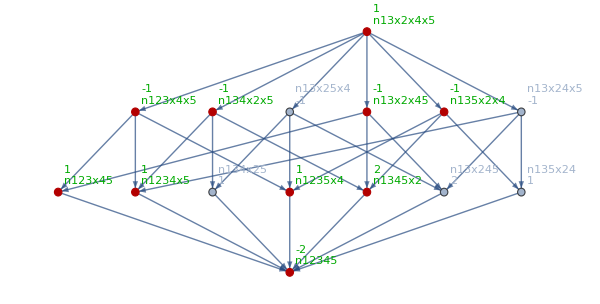

```mathematica
With[{k=quad1Key},
With[{form=allGraphs5[k,"colofourrealnull"]/.repsomething//Expand},
Graph[MobiusGraphBare[k,allGraphs5],GraphHighlight->ListofVars[form],VertexLabels->Table[v->Style[
Column[{Coefficient[form,v]
,v},Center], Darker[Green]
],{v,ListofVars[form]}]
]
]
]
```

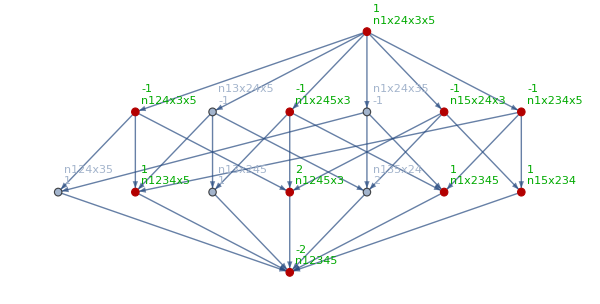

```mathematica
With[{k=quad2Key},
With[{form=allGraphs5[k,"colofourrealnull"]/.repsomething//Expand},
Graph[MobiusGraphBare[k,allGraphs5],GraphHighlight->ListofVars[form],VertexLabels->Table[v->Style[
Column[{Coefficient[form,v]
,v},Center], Darker[Green]
],{v,ListofVars[form]}]
]
]
]
```

```mathematica
Reduce[allGraphs5[gamma1Key,"colofourrealnull"]==0,n12345]
```

n12345==n124x35/2+n135x24/2+n1x2345/2-n1x24x35/2